# Bulge Chase

## Sub projects for Bulge Chase

Implement the Bulge to Spike transformation in Julia.  You need the Julia co

The Julia Schur decomposition is described at https://docs.julialang.org/en/v1/stdlib/LinearAlgebra/#LinearAlgebra.schur

First work out how to call the command and get the bits you need.

Work out how to embed the Q in a big matrix to spike a bulge of size b at the bottom of a large square matrix of size n

Work out how to embed the Q in a big matrix to spike a bulge of size b at the top of a large square matrix of size n.

Work out how to spike a bulge of size b near the middle of a large square matrix of size n.

Work out how to spike two bulges of size b near the middle of a large square matrix of size n.

It is fine to make synthetic test problems by just adding blocks to a Hessenberg reduced matrix.

Describe the spikes that result.

Extension try to work out how to sort the spike entries from large to small by absolute value! Of course you need to preserve eigenvalues.

Implement a newton method in Julia

Build a function that takes values from functions f:ℝ^n->ℝ^n and df:ℝ^n->ℝ^(n×n) with a current guess x and returns the updated x-LinearSolve[df,x].

Check and see if your code works for values from f:ℝ^n->ℝ^m and df:ℝ^n->ℝ^(m×n).  If it does not learn how to implement the minimum change solution in Julia.  If it does find documentation that it gives the min change solution.

Test your function in a script on the function plotted below.  Just define the f and df functions in Julia. I converted the df output to pretty form so that it is easier to read and/or copy and paste! You should be able to compute the single zero visible in the window.

{{(4+Cos[x1+x2]) Cos[4 x1+Sin[x1+x2]],Cos[x1+x2] Cos[4 x1+Sin[x1+x2]]},{-4 Sin[4 x1-Sin[x2]],Cos[x2] Sin[4 x1-Sin[x2]]}}

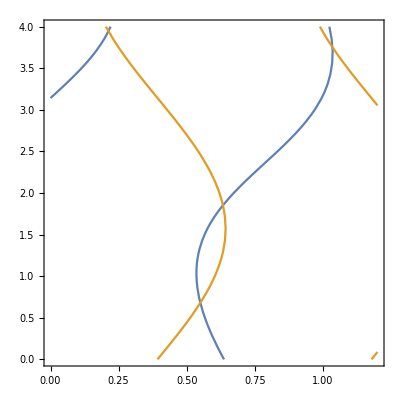

```mathematica
f[{x1_,x2_}]:= {Sin[4x1 + Sin[x1 +x2]],Cos[4 x1-Sin[x2]]}
df[{x1_,x2_}]=D[f[{x1,x2}],{{x1,x2}}]
ContourPlot[ {
f[{x1,x2}][[1]]==0,
f[{x1,x2}][[2]]==0
},{x1,0,1.2},{x2,0,4}]
```

Test your function in a script on the function below. Check it converges to a solution!

```mathematica
f[{x1_,x2_,x3_}]:= {x1 + x2+x3,Sin[x1 x2]+x3 }
 df[{x1_,x2_,x3_}]=D[f[{x1,x2,x3}],{{x1,x2,x3}}]
```

(1 | 1 | 1
x2 cos(x1 x2) | x1 cos(x1 x2) | 1)

Learn how to make a function that takes a function as argument in Julia.

Make a function that takes the functions f and df and runs Newton’s method from an initial guess until convergence.

Learn how to use an AD tool in Julia

Look on JuliaDiff for a list of AD tools.  Find one you think is well documented.  I have been using ForwardDiff.

Read the documentation.

Understand the examples.

Define the Rosenbrock function f:ℝ^n→ℝ^n from the wiki page https://en.wikipedia.org/wiki/Rosenbrock_function use the “second more involved variant”.

Use your AD tool to compute (∂f)/(∂x_1) in dimension 20 evaluated at the vector of all 1s.  Confirm that your derivative is correct in some way.  Hint plot your computed derivative against a finite difference approximation as a function of h.

Use your AD tool to compute (∂f)/(∂x_5) in dimension 22 evaluated at the vector of all 1s.  Confirm that your derivative is correct in some way.  Hint plot your computed derivative against a finite difference approximation as a function of h.

Use your AD tool to compute the directional derivative (∂f)/(∂u) where u_i=sin(i/11) in dimension 22 evaluated at the vector of all 1s.  Confirm that your derivative is correct in some way.

## First Real Question

Does the AD based Newton’s method and aggressive early deflation (AED) do any better than the standard Wilkerson shift at deflating eigenvalues at the bottom of the matrix?

We need to define a standard Wilkerson shift for an AED Implicitly Shifted Arnoldi method so that we have something to compare with our new algorithm.

This does not need to be ‘state of the art’.  In fact, it is best if it is pretty straightforward.

We need to define a our new shift procedure for an AED Implicitly Shifted Arnoldi method so that we know what we are planning to do.

It is best if it this is a straightforward modification of the comparison object.

As a reminder A is our input and throughout H is a Hessenberg matrix, B is a small block matrix, and S is a small spike matrix. A subscript top indicates the block is at the top or start (near 1,1) of the matrix. A subscript end indicates the Block or spike is at the bottom or end (near n,n) of the matrix.

A→H  with a Hessenberg decomposition. Size of matrix is n.

H→H+B_top  to incorporate a vector of shifts μ.  Size of block is b.

H+B_top→H+B_end using a sequence of Householder transformations

H+B_end→H+S_end using a Schur Decomposition

Detect and deflate suitable eigenvalues at the lower left block L of  (H+S_end) by looking at the spike.

Estimate new shifts from the bottom of the matrix L and repeat from 2.

Wilkerson Shift uses non-deflated eigenvalues of L.

Our proposed modification uses the AD based Newton predictor for the shifts.

## Finding the Spike

We need to work out how to extract the lower left matrix and the spike from the matrix.

```mathematica
{n,b}={23,6};
HB=HessenbergDecomposition[RandomReal[{-1,1},{n,n}]][[2]];
L=RandomReal[{-1,1},{b,b}];
HB⟦n-b+1;;n,n-b+1;;n⟧=L;
{Q,T}=SchurDecomposition[L];
BigQ=IdentityMatrix[n];
BigQ⟦n-b+1;;n,n-b+1;;n⟧=Q;
TabView[{
"H+B"->MatrixPlot[HB],
"Qᵀ.L.Q"->MatrixPlot[Chop[Qᵀ.L.Q]],
"Qᵀ.(H+B).Q"->MatrixPlot[Chop[BigQᵀ.HB.BigQ]]
}]
```

123

## Pivoting a Schur Decomposition

It would be nice to work out how to sort the spike so that we knew that the small entries were at the bottom. Generically sorting things in Numerical Linear Algebra is called pivoting. A row interchange is an orthogonal transformation. The matching similarity transformation switches the columns as well.

Pivot order is written down as a list of the final positions of the initial rows. Specifically
	p={3,2,4,1} 
specifies the order row_3, row_2, row_4, then row_1.  To get the matrix

```mathematica
b=4;
L=RandomReal[{-1,1},{b,b}];
p=RandomSample[Range[1,b],b]
P=IdentityMatrix[b]⟦p⟧;
TabView[{
"P"->MatrixForm[P],
"L"->MatrixForm[L],
"P.L"->MatrixForm[P.L],
"L.Pᵀ"->MatrixForm[L.Pᵀ],
"P.L.Pᵀ"->MatrixForm[P.L.Pᵀ]
},2]
```

{2,4,3,1}

12345

Since P is orthogonal the eigenvalues of P.L.Pᵀ match the eigenvalues of L!  In fact,
	T=Q.L.Qᵀ ⟹ L=Q.T.Qᵀ   then P.L.Pᵀ=P.(Q.T.Qᵀ).Pᵀ=(P.Q).T.(P.Q)ᵀ
We can reorder the rotation in the Schur Decomposition by a similarity transformation that simply reorders the rows and columns of L.

## Putting this in action.

This should let us put the spike in any order we want.  For right now lets find the spike.  The spike is the bottom b entries of the (n-b)^th column of the big transformed matrix.

```mathematica
{n,b}={23,6};
HB=HessenbergDecomposition[RandomReal[{-1,1},{n,n}]][[2]];
L=RandomReal[{-1,1},{b,b}];
HB⟦n-b+1;;n,n-b+1;;n⟧=L;
{Q,T}=SchurDecomposition[L];
BigQ=IdentityMatrix[n];
BigQ⟦n-b+1;;n,n-b+1;;n⟧=Q;
HS=Chop[BigQᵀ.HB.BigQ];
spike=HS⟦n-b+1;;n,n-b⟧;
p=Reverse[Ordering[Abs[spike]]];
P=IdentityMatrix[b]⟦p⟧;
BigQnew=IdentityMatrix[n];
BigQnew⟦n-b+1;;n,n-b+1;;n⟧=P.Q;
HBend=HB⟦n-b+1;;n,n-b+1;;n⟧;
HBp=HB;
HBp⟦n-b+1;;n,n-b+1;;n⟧=(HBp⟦n-b+1;;n,n-b+1;;n⟧)⟦p,p⟧;
HSnew=Chop[BigQnewᵀ.HBp.BigQnew];
spikenew=HSnew⟦n-b+1;;n,n-b⟧;
TabView[{
"H+B"->MatrixPlot[HB],
"Qᵀ.(H+B).Q"->MatrixPlot[HS,PlotLabel->NumberForm[spike,3]],
"Qnewᵀ.HBp.Qnew"->MatrixPlot[HSnew,PlotLabel->NumberForm[spikenew,3]]
}]
```

123